# Velocidad de Escape

En este notebook, estudiaremos el lanzamiento de un cuerpo de masa constante m desde la superficie terrestre con velocidad inicial v_0, tomando en cuenta que la fuerza gravitatoria varía con la distancia al centro de la Tierra.

La fuerza de gravedad que actúa sobre un objeto(su peso) es inversamente proporcionala al cuadrado de la distancia, es decir, si w es dicha fuerza entonces se modela en función de la distancia como:

donde x es la posición(unidimensional) del objeto respecto a la superficie terrestre, k es un parámetro y R es el radio de la Tierra. Si definimos x=0 en la superficie, entonces para x=0 la fuerza es -mg, con g la constante de gravitación al nivel del mar. Así, evaluar w en x=0 nos permite determinar el valor de k despejando la siguiente cadena de igualdades:

obteniendo

y sustituyendo en el modelo inicial obtenemos

```mathematica
.
```

## Gráfica de con el radio de la Tierra

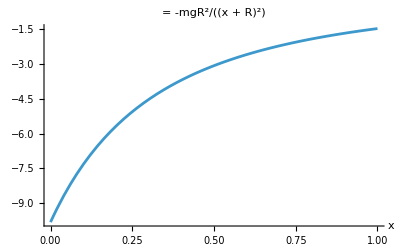

```mathematica
(* Definir constantes *)
R = 6378000;     (* Radio de la Tierra en metros *)
g = 9.81;        (* Aceleración gravitatoria en m/s^2 *)
m = 1;           (* Para ejemplo, masa unitaria (1 kg) *)

k = m*g*R^2;     (* Constante k *)

(* Graficar w(x) en cierto rango de x *)
Plot[
  -k / (x + R)^2,
  {x, 0, 1*10^7},                     (* Ajusta el rango de x según necesites *)
  PlotRange -> All,
  AxesLabel -> {"x", ""},
  PlotLabel -> " = -mgR^2/(x  +  R)^2"
]
```

## Radios y gravedad de los planetas del sistema solar

```mathematica
(* Datos de los planetas *)
planetData = <|
   "Mercurio" -> <|"R" -> 2.4397*10^6, "g" -> 3.7|>,
   "Venus"    -> <|"R" -> 6.0518*10^6, "g" -> 8.87|>,
   "Tierra"   -> <|"R" -> 6.3710*10^6, "g" -> 9.8|>,
   "Marte"    -> <|"R" -> 3.3895*10^6, "g" -> 3.71|>,
   "Júpiter"  -> <|"R" -> 6.9911*10^7, "g" -> 24.79|>,
   "Saturno"  -> <|"R" -> 5.8232*10^7, "g" -> 10.44|>,
   "Urano"    -> <|"R" -> 2.5362*10^7, "g" -> 8.87|>,
   "Neptuno"  -> <|"R" -> 2.4622*10^7, "g" -> 11.15|>
|>;""

(* Lista de nombres de los planetas (para el menú) *)
listaPlanetas = Keys[planetData];

(* Manipulate para seleccionar planeta y mostrar valores R y g *)
Manipulate[
  (* Extraemos R y g del planeta seleccionado: *)
  r = planetData[planeta]["R"];
  gg = planetData[planeta]["g"];
  
  (* Mostramos por ejemplo una expresión con R y g *)
  Column[{
    Style["Planeta seleccionado: " <> planeta, 16, Bold],
    "Radio (m): \n" <> ToString[r],
    "Gravedad (m/s^2): " <> ToString[gg],
    ""
  }],
  
  {{planeta, "Tierra", "Selecciona un planeta:"}, listaPlanetas}
]
```

```mathematica
(* Asociación con datos de cada planeta: {Radio, g} *)
planetData = <|
   "Mercurio" -> {2.4397*10^6, 3.7},
   "Venus"    -> {6.0518*10^6, 8.87},
   "Tierra"   -> {6.3710*10^6, 9.8},
   "Marte"    -> {3.3895*10^6, 3.71},
   "Júpiter"  -> {6.9911*10^7, 24.79},
   "Saturno"  -> {5.8232*10^7, 10.44},
   "Urano"    -> {2.5362*10^7, 8.87},
   "Neptuno"  -> {2.4622*10^7, 11.15}
|>;

Manipulate[
  Module[{r, gg},
   (* Extraer el radio y la gravedad según el planeta escogido *)
   {r, gg} = planetData[planeta];
   
   (* Graficar w(x) con esos valores *)
   Plot[
    - (m*gg*r^2)/((x + r)^2),
    {x, 0, 2*10^7},      (* Ajusta si deseas un rango distinto *)
    PlotRange -> All,
    AxesLabel -> {"x (m)", "w(x)"}
   ]
  ],
  {{m, 1, "Masa (kg)"}, 0.1, 100, 0.1, Appearance -> "Labeled"},
  {{planeta, "Tierra", "Planeta"}, 
    Keys[planetData], 
    ControlType -> RadioButtonBar},
  ControlPlacement -> Top
]
```

Un diagrama del fenómeno es el siguiente:

Recordemos que si  es la aceleración,  es la velocidad y  es la posición entonces las siguientes igualdades son ciertas:

Si suponemos que no hay otras fuerzas actuando en nuestro modelo podemos expresar al peso() como su descomposición en masa por aceleración quedando como:

suponiendo una masa positiva podemos cancelar m quedandonos:

.

Una forma más explicita seria:

Pero esta ecuación diferencial depende de muchas variables: la velocidad , la distancia  y el tiempo . Por lo que seria conveniente dejarla expresada en términos de solo dos de ellas. La estrategia sera ver a la velocidad  en función de la distancia  y no en función del tiempo  como esta en la ecuación. Para hacerlo usaremos la regla de la cadena en la derivada de :

que usualmente se escribe como:

Así, nuestro modelo queda como:

o análogamente

Ahora podemos aplicar separación de variables a esta ecuación para resolverla:

## Solución

Primero resolvamos la ecuación como se encuentra usualmente, que es dejando de un lado la variable dependiente() y del otro la independiente()

,	 entonces integrando ambos lados respeto a cada variable tenemos

Lo cual si integramos nos queda la siguiente igualdad:
 ,		considerando  podemos reescribir la igualdad como:

Asumiendo que la velocidad que la posición inicial es  y la velocidad inicial es  podemos encontrar el valor de  evaluando la igualdad en

así, despejando a  obtenemos    		y entonces

Ahora, si nos sentimos mal usando  como un cociente de cosas entonces podemos llegar a la misma solución con el método más riguroso, recordemos nuestro problema inicial 

la idea es la misma: integrar, pero para no modificar la igualdad integraremos respecto a la misma variable y en los mismos límites. Así, integrando respecto a la variable independiente() obtenemos la siguiente expresión:

Observemos que los limites de integración también están en términos de la variable independiente(), a saber,  y  los cuales representan la posición inicial (que ya conocemos) y la posición final (que queremos conocer) respectivamente. 
Como  solo depende de  podemos escribir sin ambigüedad

por lo que podemos escribir nuestra igualdad como:

Así, si queremos integrar lo de la izquierda habremos de encontrar una función  de forma que , una inspección a la solución con el método anterior nos dice que la función que buscamos es , así, por la regla de la cadena tendremos justo lo que queremos:

,

entonces podemos reescribir la ecuación con integrales como

o análogamente

Análogamente para el lado derecho buscamos una función  de forma que . Nuevamente mirando hacia la solución del método anterior podemos deducir que , la cual si cumple con que . Así tendremos la siguiente expresión:

Ahora, recordando el Teorema Fundamental del Cálculo podemos ver que la integral de una derivada es la función evaluada en los limites, es decir:

lo cual se simplifica a

sustituyendo las funciones  y  para regresar a nuestras variables   y

Recordando que la variable que nos interesa es la posición final ()  podemos reescribir la expresión como

y recordando que buscamos  y que , podemos despejar de la expresión quedándonos como

Que es justamente el resultado al que habíamos llegado antes! (pero sin usar diferenciales como cociente)

Observemos que el signo de la solución  nos dice si el objeto esta ascendiendo (signo positivo) o esta descendiendo(signo negativo) desde y hacia la Tierra.

## Soluciones con Mathematica

```mathematica
ClearAll["Global`*"]
```

### Soluciones simbólicas

#### Solución sin condición inicial

```mathematica
(* Ecuación: v dv/dx = -(g R^2)/(x + R)^2 *)
(* Reescrita como dv/dx == -(g R^2)/( (x+R)^2 v ) *)

solSimbolica = DSolve[
   { D[v[x], x] == - (g R^2)/( (x + R)^2 v[x]) },
   v[x],
   x
	];

solSimbolica
```

{{v[x]→-(√2 √(g R^2+R C[1]+x C[1]))/(√(R+x))},{v[x]→(√2 √(g R^2+R C[1]+x C[1]))/(√(R+x))}}

#### Solución con condición inicial v0

```mathematica
solConCI = DSolve[
   {
    D[v[x], x] == - (g R^2)/( (x + R)^2 v[x]),
    v[0] == v0
   },
   v[x],
   x
];
solConCI
```

{{v[x]→-(√(R v0^2-2 g R x+v0^2 x))/(√(R+x))},{v[x]→(√(R v0^2-2 g R x+v0^2 x))/(√(R+x))}}

### Soluciones numéricas

```mathematica
(* Definimos las constantes g, R *)
g = 9.81;
R = 6378000;

(* Definimos las constantes y la condición inicial v0, p. ej. 3000 m/s *)
v0 = 3000;

solNumerica = NDSolve[
   {
    D[v[x], x] == - (g R^2)/( (x + R)^2 v[x]),
    v[0] == v0
   },
   v,
   {x, 0, 10^4}  (* rango para x, por ejemplo 0 a 1e4 metros *)
];
```

Ahora, solNumerica es una solución numérica en forma de InterpolatingFunction.
Para evaluar  en algún punto, usamos:

```mathematica
vNum[x_] := v[x] /. solNumerica[[1]];
	
(* Ejemplo de evaluación: v(10000) *)
vNum[100]
```

2999.67

#### Gráfica de la solución numérica

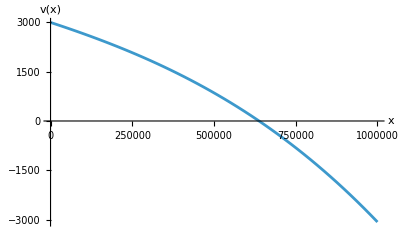

```mathematica
Plot[
  vNum[x],
  {x, 0, 10^6},
  PlotRange -> All,
  AxesLabel -> {"x", "v(x)"}
]
```

### Campo de pendientes y una solución numérica con

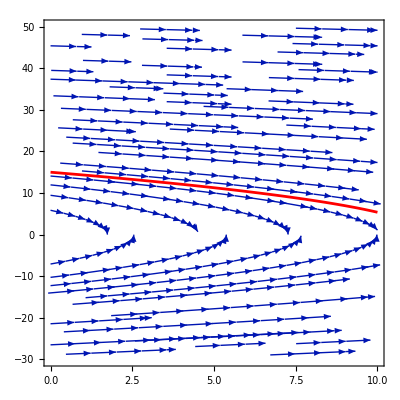

```mathematica
(* --- 1) Definir constantes y la ecuación --- *)
g = 9.81;          (* Aceleración gravitatoria en m/s^2 *)
R = 6378000;       (* Radio de la Tierra en metros *)
v0 = 15;         (* Velocidad inicial en m/s para x=0, por ejemplo *)

(* 
   Ecuación diferencial: 
   v'[x] == - (g R^2) / ((x + R)^2 * v[x])
   Para el campo de pendientes, necesitamos 
   f(x, v) = dv/dx.
*)
f[x_, v_] := - (g R^2) / ((x + R)^2 * v);

(* --- 2) Campo de pendientes con StreamPlot --- *)
slopeField = StreamPlot[
  {1, f[x, v]},   (* Vector (dx/dt, dv/dt) "ficticio" => (1, dv/dx) en el plano (x,v) *)
  {x, 0, 1*10^1}, (* Rango para x, ajústalo según necesites *)
  {v, -30, 50},   (* Rango para v, en este caso sólo velocidades positivas *)
  Frame -> True,
  FrameLabel -> {"", ""},
  PlotRange -> All,
  VectorScale -> None
];

(* --- 3) Solución numérica con NDSolve --- *)
solNumerica = NDSolve[
  {
    Derivative[1][v][x] == f[x, v[x]],
    v[0] == v0
  },
  v,
  {x, 0, 1*10^1}
];

(* Creamos una gráfica normal de v[x] en el rango 0..1e7 *)
solPlot = Plot[
  v[x] /. solNumerica,
  {x, 0, 1*10^1},
  PlotRange -> All,
  PlotStyle -> Red
];

(* --- 4) Superponer ambas gráficas --- *)
Show[slopeField, solPlot]
```

## Altura máxima y velocidad de escape

```mathematica
ClearAll["Global`*"]
```

Para determinar la altura máxima  que alcanza el cuerpo igualaremos la variable de velocidad a cero  y la variable de posición o distancia a ,   en nuestra solución encontrada, es decir:

, 		despejando a  obtenemos

```mathematica
xMax = Solve[0 == (2 g R^2)/(R + Subscript[x, max]) + Subscript[v, 0]^2 - 2 g R, Subscript[x, max]]
```

{{x_max→(R v_0^2)/(2 g R-v_0^2)}}

Así, si resolvemos la ecuación para , encontraremos la velocidad requerida para que el cuerpo alcance la distancia

```mathematica
expr = xMax[[1]][[1]][[2]]
```

(R v_0^2)/(2 g R-v_0^2)

```mathematica
v0Sol = Solve[Subscript[x, max]==expr,Subscript[v, 0]]
```

{{v_0→-(√2 √g √R √x_max)/(√(R+x_max))},{v_0→(√2 √g √R √x_max)/(√(R+x_max))}}

Como hablamos de una velocidad de escape, debemos considerar la solución positiva

```mathematica
v0Sol2 = v0Sol[[2]][[1]][[2]]
```

(√2 √g √R √x_max)/(√(R+x_max))

Así, nos queda

Finalmente la velocidad de escape el el limite cuando

```mathematica
Limit[v0Sol2,Subscript[x, max] -> Infinity]
```

√2 √g √R

Entonces, la velocidad de escape  esta dada por

Tomando en cuenta que  6378000 metros y  entonces

Hay que aclarar que este número no toma en cuenta la resistencia del aire.

### Velocidad de escape para los planetas del sistema solar

```mathematica
(* ::Section:: *)
(* Datos de los planetas *)

planetData = <|
   "Mercurio" -> <|"R" -> 2.4397*10^6, "g" -> 3.7|>,
   "Venus"    -> <|"R" -> 6.0518*10^6, "g" -> 8.87|>,
   "Tierra"   -> <|"R" -> 6.3710*10^6, "g" -> 9.8|>,
   "Marte"    -> <|"R" -> 3.3895*10^6, "g" -> 3.71|>,
   "Júpiter"  -> <|"R" -> 6.9911*10^7, "g" -> 24.79|>,
   "Saturno"  -> <|"R" -> 5.8232*10^7, "g" -> 10.44|>,
   "Urano"    -> <|"R" -> 2.5362*10^7, "g" -> 8.87|>,
   "Neptuno"  -> <|"R" -> 2.4622*10^7, "g" -> 11.15|>
|>;

(* Lista de nombres de los planetas (para el menú) *)
listaPlanetas = Keys[planetData];

(* ::Section:: *)
(* Manipulate para seleccionar planeta y calcular su velocidad de escape *)

Manipulate[
  Module[{r, gg, vEscape},
   
   (* Extraemos R y g del planeta seleccionado *)
   r = planetData[planeta]["R"];
   gg = planetData[planeta]["g"];
   
   (* Fórmula de la velocidad de escape: vEsc = Sqrt[2*g*R] *)
   vEscape = Sqrt[2 * gg * r];
   
   (* Mostramos en una columna los datos y el resultado *)
   Column[{
     Style["Planeta seleccionado: " <> planeta, 16, Bold],
     "Radio (m): \n" <> ToString[r],
     "Gravedad (m/s^2): " <> ToString[gg],
     "Velocidad de escape (m/s): " <> ToString[NumberForm[vEscape, {7,2}]]
   }]
  ],
  {{planeta, "Tierra", "Selecciona un planeta:"}, listaPlanetas}
]
```